```mathematica
EofW[A_,B_,p_]:=(1-p)*A/2+p* B/2
```

```mathematica
VofW[A_,B_,p_]:=(1-p)*A^2/3+p*B^2/3-EofW[A,B,p]^2
```

We solve the original problem (w.l.o.g. we assume A<=B):

```mathematica
Solve[EofW[A,B,p]==M/d &&VofW[A,B,p]==V/d && 1-p≥0 &&B≥A,{A,B,p},NonNegativeReals]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
{{A->ConditionalExpression[(2 M-(B d (-M^2+3 d V))/(B^2 d^2-4 B d M+3 M^2+3 d V))/(d-(d (-M^2+3 d V))/(B^2 d^2-4 B d M+3 M^2+3 d V)), V>0&&M>0&&d>M^2/(3 V)&&B≥(3 M^2+3 d V)/(2 d M)],p->ConditionalExpression[(-M^2+3 d V)/(B^2 d^2-4 B d M+3 M^2+3 d V), V>0&&M>0&&d>M^2/(3 V)&&B≥(3 M^2+3 d V)/(2 d M)]}}
```

We see that a solution only exists if d>M^2/(3 V). Further we see that, if a solution exists, we have infinitely many solutions for B (every B≥(3 M^2+3 d V)/(2 d M) is a possible choice). For every possible choice of B there a unique solution for A and p given above. 
In the next step we see that if we additionally want A>0 to hold, we just need to choose a value for B which is at least by an arbitrarily small but positive epsilon larger than the minimal possible choice of B.
We see this by observing that when we add A>0 as an constraint, the only difference in the solution is that B is given by a strict inequality B>... instead of B≥... :

```mathematica
Solve[EofW[A,B,p]==M/d &&VofW[A,B,p]==V/d && 1-p≥0 &&B≥A&&A>0,{A,B,p},NonNegativeReals]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
{{A->ConditionalExpression[(2 M-(B d (-M^2+3 d V))/(B^2 d^2-4 B d M+3 M^2+3 d V))/(d-(d (-M^2+3 d V))/(B^2 d^2-4 B d M+3 M^2+3 d V)), V>0&&M>0&&d>M^2/(3 V)&&B>(3 M^2+3 d V)/(2 d M)],p->ConditionalExpression[(-M^2+3 d V)/(B^2 d^2-4 B d M+3 M^2+3 d V), V>0&&M>0&&d>M^2/(3 V)&&B>(3 M^2+3 d V)/(2 d M)]}}
```

Our choice of B is:

```mathematica
Bchoice:=If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],2*M/d]
```

, where the first case is motivated by the arguments above and the second case guarantees the correct expectation as we will prove later.
This uniquely defines p and A as in the paper by plugging B into the formulas for A and p above (in the case a solution exists). In the other cases we also make specific choices.

```mathematica
pchoice:=With[{B=Bchoice},If[d>M^2/(3 V),(-M^2+3 d V)/(B^2 d^2-4 B d M+3 M^2+3 d V),1]]
```

We see that in the formula for A given above the expression for p appears, so we can use an easier expression for A:

```mathematica
Achoice:=With[{B=Bchoice,p=pchoice},If[d>M^2/(3 V),(2 M-B d p)/(d (1-p)),0]]
```

Now we can check if our chosen solution fulfills all the desired properties.

## Proof of item 1:

```mathematica
Simplify[EofW[Achoice,Bchoice,pchoice]]
```

M/d

## Proof of item 2 and 3:

We use Mathematica for this proof since the terms can get quite complicated:

```mathematica
VofW[Achoice,Bchoice,pchoice]
```

1/3 (1-If[d>M^2/(3 V),(-M^2+3 d V)/(If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d]^2 d^2-4 If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d] d M+3 M^2+3 d V),1]) If[d>M^2/(3 V),(2 M-If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d] d If[d>M^2/(3 V),(-M^2+3 d V)/(If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d]^2 d^2-4 If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d] d M+3 M^2+3 d V),1])/(d (1-If[d>M^2/(3 V),(-M^2+3 d V)/(If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d]^2 d^2-4 If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d] d M+3 M^2+3 d V),1])),0]^2+1/3 If[d>M^2/(3 V),(-M^2+3 d V)/(If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d]^2 d^2-4 If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d] d M+3 M^2+3 d V),1] If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d]^2-(1/2 (1-If[d>M^2/(3 V),(-M^2+3 d V)/(If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d]^2 d^2-4 If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d] d M+3 M^2+3 d V),1]) If[d>M^2/(3 V),(2 M-If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d] d If[d>M^2/(3 V),(-M^2+3 d V)/(If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d]^2 d^2-4 If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d] d M+3 M^2+3 d V),1])/(d (1-If[d>M^2/(3 V),(-M^2+3 d V)/(If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d]^2 d^2-4 If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d] d M+3 M^2+3 d V),1])),0]+1/2 If[d>M^2/(3 V),(-M^2+3 d V)/(If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d]^2 d^2-4 If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d] d M+3 M^2+3 d V),1] If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],(2 M)/d])^2

But Mathematica can easily simplify complicated terms such as this one:

```mathematica
Simplify[VofW[Achoice,Bchoice,pchoice]]
```

Piecewise[{{M^2/(3 d^2), 3 d V^2≤M^2 V}, {V/d, True}}]

This is even true for V≥0, but it can be slightly further simplified if V>0:

```mathematica
Assuming[V>0,Simplify[VofW[Achoice,Bchoice,pchoice]]]
```

Piecewise[{{M^2/(3 d^2), 3 d V≤M^2}, {V/d, 3 d V>M^2}, {Indeterminate, True}}]

We see that the V/d≤VofW holds always true (for d>0) and V/d=VofW if d>M^2/(3 V) or we can check it in the next line:

```mathematica
Reduce[V/d≤Simplify[VofW[Achoice,Bchoice,pchoice]]&&V>0&&d>0&&M>0]
```

V>0&&M>0&&d>0

## Proof of item 4:

```mathematica
Reduce[0<Simplify[Achoice,d>M^2/(3 V)]&&V>0&&d>0&&M>0&&epsilon>0&&d>M^2/(3 V)]
```

Binit∈ℝ&&V>0&&M>0&&d>M^2/(3 V)&&epsilon>0

## Proof of item 5:

```mathematica
Reduce[0==Simplify[Achoice,d>M^2/(3 V)]&&V>0&&d>0&&M>0&&epsilon==0&&Binit≤ Simplify[Bchoice,d>M^2/(3 V)]&&d>M^2/(3 V)]
```

V>0&&M>0&&d>M^2/(3 V)&&Binit≤(3 M^2+3 d V)/(2 d M)&&epsilon==0

(In the case of d≤M^2/(3 V), Achoice is zero anyway. Note that Binit<Bchoice implies Binit≤(3 M^2+3 d V)/(2 d M) for epsilon==0.)

## Proof of item 6:

```mathematica
Reduce[0≤ Simplify[Achoice,d>M^2/(3 V)]&&V>0&&d>0&&M>0&&epsilon≥ 0&&Binit≥0&&d>M^2/(3 V)]
```

V>0&&M>0&&d>M^2/(3 V)&&Binit≥0&&epsilon≥0

```mathematica
Reduce[0≤ Simplify[Bchoice,d>M^2/(3 V)]&&V>0&&d>0&&M>0&&epsilon≥ 0&&Binit≥0&&d>M^2/(3 V)]
```

V>0&&M>0&&d>M^2/(3 V)&&epsilon≥0&&Binit≥0

## Proof of item 7: (A ≤B)

```mathematica
Reduce[ Simplify[Achoice,d>M^2/(3 V)]≤ Simplify[Bchoice,d>M^2/(3 V)]&&V>0&&d>0&&M>0&&epsilon≥ 0&&Binit≥0&&d>M^2/(3 V)]
```

V>0&&M>0&&d>M^2/(3 V)&&epsilon≥0&&Binit≥0

## Proof of item 8:

```mathematica
Reduce[(3V)/(2M)≤ Simplify[Bchoice,d>M^2/(3 V)]&&V>0&&d>0&&M>0&&epsilon≥ 0&&Binit≥0&&d>M^2/(3 V)]
```

V>0&&M>0&&d>M^2/(3 V)&&Binit≥0&&epsilon≥0

```mathematica
Reduce[(3V)/(2M)≤ Simplify[Bchoice,d<=M^2/(3 V)]&&V>0&&d>0&&M>0&&epsilon≥ 0&&Binit≥0&&d<=M^2/(3 V)]
```

epsilon≥0&&Binit≥0&&V>0&&M>0&&0<d≤M^2/(3 V)

## Proof of item 9:

```mathematica
Assuming[V>0&&M>0&&epsilon≥ 0&&Binit≥0,Limit[Bchoice,d->∞]]
```

Piecewise[{{Binit, 2 Binit M>3 V}, {(3 V)/(2 M), True}}]

## Visualizations:

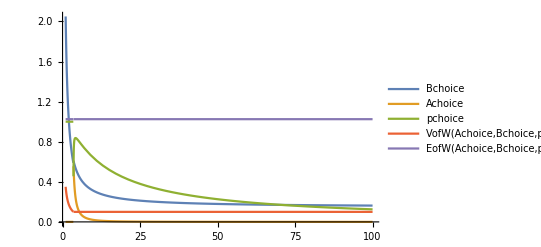

```mathematica
M:=1.025
V:=1/10
Binit := 0.05
epsilon := 0.1
Plot[{Bchoice,Achoice,pchoice,VofW[Achoice,Bchoice,pchoice]*d,EofW[Achoice,Bchoice,pchoice]*d},{d,1,100},PlotLegends->"Expressions"]
Clear[M,V,Binit,epsilon]
```

```mathematica
Manipulate[Plot[{If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],2*M/d],ReplaceAll[If[d>M^2/(3 V),(-M^2+3 d V)/(B^2 d^2-4 B d M+3 M^2+3 d V),1],B->If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],2*M/d]],ReplaceAll[If[d>M^2/(3 V),(2 M-(B d (-M^2+3 d V))/(B^2 d^2-4 B d M+3 M^2+3 d V))/(d-(d (-M^2+3 d V))/(B^2 d^2-4 B d M+3 M^2+3 d V)),0],B->If[d>M^2/(3 V),Max[(3 M^2+3 d V)/(2 M d)+epsilon/d,Binit],2*M/d]],Piecewise[{{M^2/(3 d^2), 3 d V≤M^2}, {V/d, 3 d V>M^2}, {Indeterminate, True}}]*d,M/d*d},{d,1,dMax},PlotLegends->{"B","p","A","V*d","E*d"}],{M,1,2},{V,1/50,1},{Binit,0,0.1},{epsilon,0,0.2},{dMax,10,1000}]
```